```mathematica
p[X_,k1_,n1_,b1_]:=b1*X^n1/(k1^n1+X^n1);
q[X_,k2_,n2_,b2_]:= b2*k2^n2/(k2^n2+X^n2);
```

```mathematica
dSusceptibles[TotalP_,Susceptibles_,Infected_,Confined_, k2_, n2_, b2_, beta_]:=- beta * Susceptibles*Infected /TotalP+ q[Infected,k2,n2,b2]*Confined-p[Infected,k2,n2,b2]*Susceptibles;
dConfined[TotalP_,Susceptibles_,Confined_, Infected_, k2_, n2_, b2_]:=p[Infected,k2,n2,b2]*Susceptibles -q[Infected,k2,n2,b2]*Confined;
dInfected[TotalP_,Susceptibles_,Infected_, beta_, rmu_]:=beta * Susceptibles*Infected /TotalP  - Infected*rmu;
dRecovered[Infected_, rmu_]:= rmu*Infected;
Conservation[Susceptibles_,Infected_,Confined_,Recovered_] := Susceptibles+Infected+Confined+Recovered;
```

```mathematica
FullSimplify[Solve[{- beta * Susceptibles*Infected /TotalP==0,
dInfected[TotalP, Susceptibles,Infected, beta, rmu]==0,
dConfined[TotalP,Susceptibles,Confined, Infected, k2, n2, b2] ==0,
dRecovered[Infected, rmu] == 0,
Conservation[Susceptibles,Infected,Confined,Recovered]==TotalP},{Susceptibles,Infected,Confined,Recovered}],Assumptions->{ Susceptibles≥ 0,Infected≥ 0, Confined ≥0, Recovered≥0, TotalP >0, Susceptibles≤ TotalP, k1≥0,k2≥0, n1≥ 1, n2≥1, b1≥0,b2≥0, rmu≥ 0, beta>0}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -(Infected^n2)^(1/n2) == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Infected→0,Confined→0,Recovered→-Susceptibles+TotalP},{Susceptibles→0,Infected→0,Confined→0,Recovered→TotalP},{Susceptibles→(rmu TotalP)/beta,Infected→0,Confined→0,Recovered→TotalP-(rmu TotalP)/beta}}

```mathematica
(*Equilibria*)
FullSimplify[Solve[{dSusceptibles[TotalP,Susceptibles,Infected,Confined, k2, n2, b2, beta]==0,
dInfected[TotalP, Susceptibles,Infected, beta, rmu]==0,
dRecovered[Infected, rmu] == 0,
Susceptibles+Infected+Recovered==TotalP},{Susceptibles,Infected,Confined,Recovered}],Assumptions->{ Susceptibles≥ 0,Infected≥ 0, Confined ≥0, Recovered≥0, TotalP >0, Susceptibles≤ TotalP, k1≥0,k2≥0, n1≥ 1, n2≥1, b1≥0,b2≥0, rmu≥ 0, beta>0}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -(Infected^n2)^(1/n2) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -(Infected^(1+n2))^(1/(1+n2)) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -(Infected^n2)^(1/n2) == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Infected→0,Confined→0,Recovered→-Susceptibles+TotalP},{Susceptibles→(rmu TotalP)/beta,Infected→0,Confined→0,Recovered→TotalP-(rmu TotalP)/beta}}

```mathematica
(*Jacobian*)
a = {dSusceptibles[TotalP,Susceptibles,Infected,Confined, k2, n2, b2,beta],
       dInfected[TotalP, Susceptibles,Infected, beta, rmu],
dConfined[TotalP,Susceptibles,Confined, Infected, k2, n2, b2],
dRecovered[Infected, rmu]}
b = {Susceptibles,Infected,Confined,Recovered}
```

{(b2 Confined k2^n2)/(Infected^n2+k2^n2)-(b2 Infected^n2 Susceptibles)/(Infected^n2+k2^n2)-(beta Infected Susceptibles)/TotalP,-Infected rmu+(beta Infected Susceptibles)/TotalP,-(b2 Confined k2^n2)/(Infected^n2+k2^n2)+(b2 Infected^n2 Susceptibles)/(Infected^n2+k2^n2),Infected rmu}

{Susceptibles,Infected,Confined,Recovered}

```mathematica
JacobianSCIR =FullSimplify[Limit[Limit[Limit[Limit[D[a,{b}],
Confined->0],
Infected->0],
Recovered->(TotalP-cte)],
Susceptibles->cte]
,Assumptions->{  Susceptibles≥ 0,Infected≥ 0, Confined ≥0, Recovered≥0, TotalP >0, Susceptibles≤ TotalP, k2≥0, n2≥1,b2≥0, rmu≥ 0, beta>0}]
```

{{ConditionalExpression[0, n2>1],-(beta cte)/TotalP,b2,0},{0,-rmu+(beta cte)/TotalP,0,0},{0,ConditionalExpression[0, cte∈ℝ&&n2>1],-b2,0},{0,rmu,0,0}}

```mathematica
MatrixForm[JacobianSCIR]
FullSimplify[Eigenvalues[JacobianSCIR]]
```

(ConditionalExpression[0, n2>1] | -(beta cte)/TotalP | b2 | 0
0 | -rmu+(beta cte)/TotalP | 0 | 0
0 | ConditionalExpression[0, cte∈ℝ&&n2>1] | -b2 | 0
0 | rmu | 0 | 0)

{0,-b2,-rmu+(beta cte)/TotalP,ConditionalExpression[0, n2>1]}

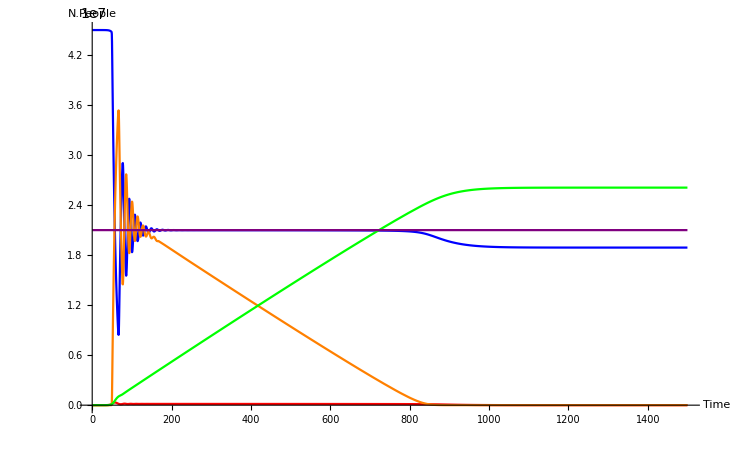

```mathematica
(*Some numerical integrations and plots that dont appear in the text*)
S0 = 44999999;
I0 = 1;
C0 = 0;
R0 = 0;
Tfinal=1500;
n1=20;
n2=20;
b1=0.1;
b2=0.1;
k1=150000;
k2=150000;
beta =0.45;
TotalP= 45000000;
rmu =0.21;
Plot[Evaluate[First[{Susceptibles[t],Infected[t], Confined[t], Recovered[t], Hion[t]} /. NDSolve[{
Susceptibles'[t]==- beta * Susceptibles[t]*Infected[t] /TotalP+ q[Infected[t] ,k2,n2,b2]*Confined[t]-p[Infected[t] ,k1,n1,b1]*Susceptibles[t],
Infected'[t]==beta * Susceptibles[t]*Infected[t] /TotalP  - Infected[t]*rmu,
Confined'[t]==p[Infected[t] ,k1,n1, b1]*Susceptibles[t] -q[Infected[t],k2,n2,b2]*Confined[t],
Recovered'[t]== rmu*Infected[t],
Hion'[t]==0,
Susceptibles[0]==S0,Infected[0]==I0, Confined[0]==C0, Recovered[0] == R0, Hion[0]==rmu*TotalP/beta},{Susceptibles,Infected, Confined, Recovered,Hion},{t,0,Tfinal}]]],{t,0,Tfinal},PlotStyle->{Blue,Red, Orange, Green, Purple},PlotRange->All, AxesLabel->{"Time","N.People"}]
```

```mathematica
g1 =ContourPlot3D[{dSusceptibles[TotalP,Susceptibles,Infected,Confined, k1, n1,b1, k2, n2, b2, beta]==0,
dConfined[TotalP,Susceptibles,Confined, Infected, k1, n1, b1, k2, n2, b2]==0,
dInfected[TotalP,Susceptibles,Infected, beta, rmu]==0},{Susceptibles,0,10000000},{Confined,0,30000000},{Infected,0,2000000}
,Mesh->None,ContourStyle->{Red,Green,Blue},AxesLabel->{"S","C","I"}]
```

-Graphics3D-

```mathematica
S0 = 44999999;
I0 = 1;
C0 = 0;
R0 = 0;
Tfinal=1000;
sol = NDSolve[{Susceptibles'[t]==- beta * Susceptibles[t]*Infected[t] /TotalP+ q[Infected[t] ,k2,n2,b2]*Confined[t]-p[Infected[t] ,k1,n1,b1]*Susceptibles[t],
Infected'[t]==beta * Susceptibles[t]*Infected[t] /TotalP  - Infected[t]*rmu,
Confined'[t]==p[Infected[t] ,k1,n1, b1]*Susceptibles[t] -q[Infected[t],k2,n2,b2]*Confined[t],Susceptibles[0]==S0,Infected[0]==I0, Confined[0]==C0},{Susceptibles,Infected, Confined},{t,0,Tfinal}]

g2=ParametricPlot3D[ {Susceptibles[t],Confined[t],Infected[t]}/. sol ,{t,0,Tfinal},PlotRange->{{0,10000000},{0,30000000},{0,2000000}},AxesLabel->{"S","I","C"},PlotStyle->{Orange,Thick}]
```

{{Susceptibles→InterpolatingFunction[…],Infected→InterpolatingFunction[…],Confined→InterpolatingFunction[…]}}

-Graphics3D-

```mathematica
Show[g1,g2]
```

-Graphics3D-